```mathematica
otext = "Artificial intelligence (AI) is intelligence demonstrated by computers, as opposed to human or animal intelligence. "Intelligence" encompasses the ability to learn and to reason, to generalize, and to infer meaning.AI applications include advanced web search engines (e.g., Google Search), recommendation systems (used by YouTube, Amazon, and Netflix), understanding human speech (such as Siri and Alexa), self-driving cars (e.g., Waymo), generative or creative tools (ChatGPT and AI art), automated decision-making, and competing at the highest level in strategic game systems (such as chess and Go).Artificial intelligence was founded as an academic discipline in 1956, and in the years since it has experienced several waves of optimism, followed by disappointment and the loss of funding (known as an "AI winter"), followed by new approaches, success, and renewed funding. AI research has tried and discarded many different approaches, including simulating the brain, modeling human problem solving, formal logic, large databases of knowledge, and imitating animal behavior. In the first decades of the 21st century, highly mathematical and statistical machine learning has dominated the field, and this technique has proved highly successful, helping to solve many challenging problems throughout industry and academia.The various sub-fields of AI research are centered around particular goals and the use of particular tools. The traditional goals of AI research include reasoning, knowledge representation, planning, learning, natural language processing, perception, and the ability to move and manipulate objects. General intelligence (the ability to solve an arbitrary problem) is among the field's long-term goals. To solve these problems, AI researchers have adapted and integrated a wide range of problem-solving techniques, including search and mathematical optimization, formal logic, artificial neural networks, and methods based on statistics, probability, and economics. AI also draws upon computer science, psychology, linguistics, philosophy, and many other fields.
The field was founded on the assumption that human intelligence "can be so precisely described that a machine can be made to simulate it". This raised philosophical arguments about the mind and the ethical consequences of creating artificial beings endowed with human-like intelligence; these issues have previously been explored by myth, fiction (science fiction), and philosophy since antiquity. Computer scientists and philosophers have since suggested that AI may become an existential risk to humanity if its rational capacities are not steered towards goals beneficial to humankind. Economists have frequently highlighted the risks of redundancies from AI, and speculated about unemployment if there is no adequate social policy for full employment. The term artificial intelligence has also been criticized for overhyping AI's true technological capabilities.

Artificial beings with intelligence appeared as storytelling devices in antiquity, and have been common in fiction, as in Mary Shelley's Frankenstein or Karel Čapek's R.U.R. These characters and their fates raised many of the same issues now discussed in the ethics of artificial intelligence.The study of mechanical or "formal" reasoning began with philosophers and mathematicians in antiquity. The study of mathematical logic led directly to Alan Turing's theory of computation, which suggested that a machine, by shuffling symbols as simple as "0" and "1", could simulate any conceivable act of mathematical deduction. This insight that digital computers can simulate any process of formal reasoning is known as the Church–Turing thesis. This, along with concurrent discoveries in neurobiology, information theory and cybernetics, led researchers to consider the possibility of building an electronic brain. The first work that is now generally recognized as AI was McCullouch and Pitts' 1943 formal design for Turing-complete "artificial neurons".The field of AI research was born at a workshop at Dartmouth College in 1956. The attendees became the founders and leaders of AI research. They and their students produced programs that the press described as "astonishing": computers were learning checkers strategies, solving word problems in algebra, proving logical theorems and speaking English. 
By the middle of the 1960s, research in the U.S. was heavily funded by the Department of Defense and laboratories had been established around the world.Researchers in the 1960s and the 1970s were convinced that their methods would eventually succeed in creating a machine with artificial general intelligence and considered this the goal of their field. Herbert 
";
```

```mathematica
rareWordsFinder = 
 LLMFunction[
  "Find rare words in the passage and put them in a list {\"word1\",...}:``", "Expression"]
```

LLMFunction[…]

```mathematica
foundWords = rareWordsFinder[otext]
```

{rare,passage}

```mathematica
Column@foundWords
```

rare
passage

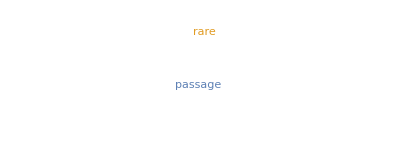

```mathematica
WordCloud[foundWords]
```